```mathematica
export[name_]:=Export["E:\\GDrive\\GitHub\\code\\classes\\cs546\\pa2\\objects\\"<>name<>".obj",ExampleData[{"Geometry3D",name}]]
```

```mathematica
ExampleData["Geometry3D"]
```

{{Geometry3D,BassGuitar},{Geometry3D,Beethoven},{Geometry3D,CastleWall},{Geometry3D,Cone},{Geometry3D,Cow},{Geometry3D,Deimos},{Geometry3D,Galleon},{Geometry3D,HammerheadShark},{Geometry3D,Horse},{Geometry3D,KleinBottle},{Geometry3D,MoebiusStrip},{Geometry3D,Phobos},{Geometry3D,PottedPlant},{Geometry3D,Seashell},{Geometry3D,SedanCar},{Geometry3D,SpaceShuttle},{Geometry3D,StanfordBunny},{Geometry3D,Torus},{Geometry3D,Tree},{Geometry3D,Triceratops},{Geometry3D,Tugboat},{Geometry3D,UtahTeapot},{Geometry3D,UtahVWBug},{Geometry3D,Vase},{Geometry3D,VikingLander},{Geometry3D,Wrench},{Geometry3D,Zeppelin}}

```mathematica
ExampleData[{"Geometry3D","Cone"}]
```

-Graphics3D-

```mathematica
export/@ExampleData["Geometry3D"]⟦All,2⟧
```

{E:\GDrive\GitHub\code\classes\cs546\pa2\objects\BassGuitar.obj,E:\GDrive\GitHub\code\classes\cs546\pa2\objects\Beethoven.obj,E:\GDrive\GitHub\code\classes\cs546\pa2\objects\CastleWall.obj,E:\GDrive\GitHub\code\classes\cs546\pa2\objects\Cone.obj,E:\GDrive\GitHub\code\classes\cs546\pa2\objects\Cow.obj,E:\GDrive\GitHub\code\classes\cs546\pa2\objects\Deimos.obj,E:\GDrive\GitHub\code\classes\cs546\pa2\objects\Galleon.obj,E:\GDrive\GitHub\code\classes\cs546\pa2\objects\HammerheadShark.obj,E:\GDrive\GitHub\code\classes\cs546\pa2\objects\Horse.obj,E:\GDrive\GitHub\code\classes\cs546\pa2\objects\KleinBottle.obj,E:\GDrive\GitHub\code\classes\cs546\pa2\objects\MoebiusStrip.obj,E:\GDrive\GitHub\code\classes\cs546\pa2\objects\Phobos.obj,E:\GDrive\GitHub\code\classes\cs546\pa2\objects\PottedPlant.obj,E:\GDrive\GitHub\code\classes\cs546\pa2\objects\Seashell.obj,E:\GDrive\GitHub\code\classes\cs546\pa2\objects\SedanCar.obj,E:\GDrive\GitHub\code\classes\cs546\pa2\objects\SpaceShuttle.obj,E:\GDrive\GitHub\code\classes\cs546\pa2\objects\StanfordBunny.obj,E:\GDrive\GitHub\code\classes\cs546\pa2\objects\Torus.obj,E:\GDrive\GitHub\code\classes\cs546\pa2\objects\Tree.obj,E:\GDrive\GitHub\code\classes\cs546\pa2\objects\Triceratops.obj,E:\GDrive\GitHub\code\classes\cs546\pa2\objects\Tugboat.obj,E:\GDrive\GitHub\code\classes\cs546\pa2\objects\UtahTeapot.obj,E:\GDrive\GitHub\code\classes\cs546\pa2\objects\UtahVWBug.obj,E:\GDrive\GitHub\code\classes\cs546\pa2\objects\Vase.obj,E:\GDrive\GitHub\code\classes\cs546\pa2\objects\VikingLander.obj,E:\GDrive\GitHub\code\classes\cs546\pa2\objects\Wrench.obj,E:\GDrive\GitHub\code\classes\cs546\pa2\objects\Zeppelin.obj}

```mathematica
export["SedanCar"]
```

E:\GDrive\GitHub\code\classes\cs546\pa2\objects\StanfordBunny.obj

```mathematica
polygons=ExampleData[{"Geometry3D",model},"PolygonData"];
```

```mathematica
ExampleData[{"Geometry3D",model},"Properties"]
```

{Graphics3D,GraphicsComplex,Name,PolygonCount,PolygonData,PolygonObjects,VertexData,VertexNormals}

```mathematica
model="Horse";
```

```mathematica
vertices=Rescale[ExampleData[{"Geometry3D",model},"VertexData"]];
gc=ExampleData[{"Geometry3D",model},"GraphicsComplex"];
gc⟦1⟧=Rescale[vertices];
Export["E:\\GDrive\\GitHub\\code\\classes\\cs546\\pa2\\objects\\"<>model<>".obj",Graphics3D[gc]]
```

E:\GDrive\GitHub\code\classes\cs546\pa2\objects\Horse.obj

```mathematica
Graphics3D[gc,Axes->True]
```

-Graphics3D-

```mathematica
Import["E:\\GDrive\\GitHub\\code\\classes\\cs546\\pa2\\objects\\"<>model<>".obj"]
```

-Graphics3D-

```mathematica
{{rx1,rx2},{ry1,ry2},{rz1,rz2}}={Min[#],Max[#]}&/@Transpose[vertices]
```

{{-4.64855,4.64855},{-3.34742,3.31909},{-6.03088,5.54417}}

```mathematica
rx=rx2-rx1
ry=ry2-ry1
rz=rz2-rz1
```

9.2971

6.66651

11.5751

```mathematica
rm=Max[rx,ry,rz]
```

11.5751

```mathematica
Export["E:\\GDrive\\Classes\\Computer Graphics\\91546s2015_Richard_Hennigan_pa2\\objects\\UtahTeapot.obj",ExampleData[{"Geometry3D","UtahTeapot"}]]
```

E:\GDrive\Classes\Computer Graphics\91546s2015_Richard_Hennigan_pa2\objects\UtahTeapot.obj

```mathematica
Export["E:\\GDrive\\Classes\\Computer Graphics\\91546s2015_Richard_Hennigan_pa2\\objects\\SpaceShuttle.obj",ExampleData[{"Geometry3D","SpaceShuttle"}]]
```

E:\GDrive\Classes\Computer Graphics\91546s2015_Richard_Hennigan_pa2\objects\SpaceShuttle.obj

```mathematica
Export["E:\\GDrive\\Classes\\Computer Graphics\\91546s2015_Richard_Hennigan_pa2\\objects\\BassGuitar.obj",ExampleData[{"Geometry3D","BassGuitar"}]]
```

E:\GDrive\Classes\Computer Graphics\91546s2015_Richard_Hennigan_pa2\objects\BassGuitar.obj

```mathematica
Union[Length/@polygons]
```

{3,4}

```mathematica
lines=Union[Sort/@Flatten[Partition[#,2,1,1]&/@polygons,1]];
```

```mathematica
vertices
```

```mathematica
lines
```

{{1,2},{1,3},{1,238},{1,315},{1,317},{1,318},{1,358},{2,3},{2,8},{2,237},{2,238},{3,9},{3,361},{4,5},{4,6},{4,10},{4,240},{4,241},{5,6},{5,240},{5,316},{5,319},2233,{1108,1109},{1108,1110},{1108,1111},{1109,1112},{1110,1113},{1111,1112},{1111,1113},{1112,1114},{1113,1115},{1114,1116},{1115,1117},{1116,1118},{1117,1119},{1126,1127},{1128,1129},{1130,1131},{1130,1134},{1132,1133},{1132,1135},{1134,1136},{1135,1137},{1146,1147}}
 |  |  |  |

```mathematica
triangles=Flatten[If[Length[#]==4,{#⟦{1,2,3}⟧,#⟦{1,3,4}⟧},{#}]&/@polygons,1];
```

```mathematica
Graphics3D[GraphicsComplex[vertices,Polygon@triangles]]
```

-Graphics3D-

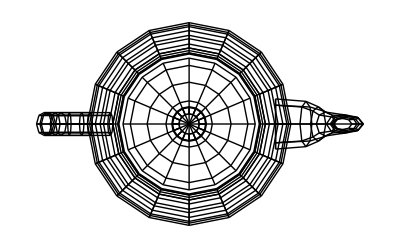

```mathematica
xy=Graphics[GraphicsComplex[vertices⟦All,{1,2}⟧,Line/@lines]]
```

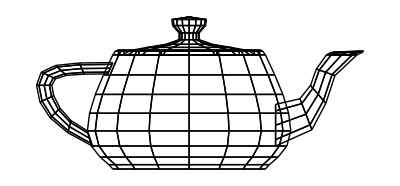

```mathematica
xz=Graphics[GraphicsComplex[vertices⟦All,{1,3}⟧,Line/@lines]]
```

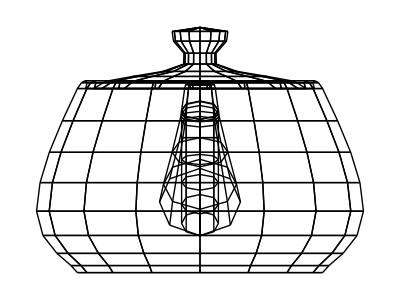

```mathematica
yz=Graphics[GraphicsComplex[vertices⟦All,{2,3}⟧,Line/@lines]]
```